# PROGRAMA DE PAT - EUREKA 4.1

## Início

```mathematica
Clear["Global`*"]
```

```mathematica
SetDirectory[NotebookDirectory[]]
```

/Users/acsl/Downloads

```mathematica
SetOptions[{ListPlot,ListLogPlot,ListLogLogPlot},BaseStyle->{FontFamily->"Helvetica", 14},ImageSize-> 600,Joined-> True,PlotStyle-> Thick,
Axes-> False,Frame-> True];
```

## Datos

```mathematica
sigma1=0;                (* ro1 = Resistividad Primer Estrato *)
ϵ1=8.854 10^-12;
μ=4. π 10^-7;

ro2=2000;                (* ro2 = input ('Resistividad Segundo Estrato *)
sigmasolo=1/ro2;
alfa=0.706;
deltai=11.71/1000;
kprima=sigmasolo+(deltai)(Cot[(Pi/2)*(alfa)]+I)*(ω/(2*1000000*π))^alfa;
sigma2=Re[kprima];
ϵ2=Im[kprima]/ω;
(*sigma2=sigmasolo;
ϵ2=100ϵ1;*)

H=0.5;                   (* H = Profundidad enterramiento de la Red *)
rh=0.01;            (* rh=input ('radio de conductor horizontal *)
rv=0.01;             (* rv=input ('Radio de varilla vertical *)
L=4;
```

```mathematica
(*Datos de Electrodo Horizontal y vertical*)
SPH1M={{37.071 , 7.071,-H},{30,0,-H},{20,  0,-H},{10,  0,-H},{37.071,11.571,-H},{30,18.642,-H},{20,18.642,-H},{10,18.642,-H},{41.571,7.071,-H},{48.642,0         ,-H},{58.642,0         ,-H},{68.642,0         ,-H},{41.571,11.571,-H},{48.642,18.642,-H},{58.642,18.642,-H},{68.642,18.642,-H}};  
SPH2M={{30          ,           0,-H},{20,  0,-H},{10,  0,-H},{0,  0,-H},{30         ,18.642,-H},{20,18.642,-H},{10   ,18.642,-H},{0,18.642,-H},{48.642,0         ,-H},{58.642,0         ,-H},{68.642,0         ,-H},{78.642,0         ,-H},{48.642,18.642,-H},{58.642,18.642,-H},{68.642,18.642,-H},{78.642,18.642,-H}};
SPV1M={};
SPV2M={};
```

```mathematica
Ninyecc1={{37.071 , 7.071,-H},{37.071,11.571,-H},{41.571,7.071,-H},{41.571,11.571,-H}};
```

## Graficador

```mathematica
Module [{LSPH1M=Length[SPH1M],LSPV1M=Length[SPV1M]},
GrH=Table[{SPH1M[[n,p]]+(SPH2M[[n,p]]-SPH1M[[n,p]])*t},{n,1,LSPH1M},{p,1,3}];GrV=Table[{SPV1M[[n,p]]+(SPV2M[[n,p]]-SPV1M[[n,p]])*t},{n,1,LSPV1M},{p,1,3}];
];
```

```mathematica
If[ GrV≠{},ParametricPlot3D[{GrH,GrV},{t,0,1}],ParametricPlot3D[GrH,{t,0,1}]]
```

-Graphics3D-

## Rutinas Auxiliares (Segmentador, RPT, etc)

```mathematica
segs[SP1_List,SP2_List,NS_Real,r_Real]:=Module[
{LSPH1M,LSGM,LTotal,RP12C,SP1NS,SP2NS,SP12C,SP1XI,SP2XI,vectorr,SP12XI,radius,LSmatriz},
LSPH1M=Length[SP1];
LSGM=Norm[(SP2-SP1)[[#,All]]]&/@Range[1,LSPH1M];
LTotal=Total[LSGM];
SP1NS=Flatten[Table[SP1[[i,All]]+(#/NS)*(SP2[[i,All]]-SP1[[i,All]])&/@Range[0,NS-1],{i,1,LSPH1M}],1];
SP2NS=Flatten[Table[SP1[[i,All]]+((#+1)/NS)*(SP2[[i,All]]-SP1[[i,All]])&/@Range[0,NS-1],{i,1,LSPH1M}],1];
SP12C=(SP1NS+SP2NS)/2;
vectorr=Cross[{1,0,0},(SP2NS-SP1NS)[[#]]]&/@Range[1,NS*LSPH1M];
If[Norm[vectorr[[#]]]==0,vectorr[[#]]=Cross[{0,1,0},(SP2NS-SP1NS)[[#]]],vectorr[[#]]]&/@Range[1,NS*LSPH1M];
If[vectorr[[#,3]]<0,vectorr[[#]]=-vectorr[[#]],vectorr[[#]]]&/@Range[1,NS*LSPH1M];
SP12XI=SP12C[[#]]+r*Normalize[vectorr[[#]]]&/@Range[1,NS*LSPH1M];
SP1XI=SP1NS[[#]]+r*Normalize[vectorr[[#]]]&/@Range[1,NS*LSPH1M];
SP2XI=SP2NS[[#]]+r*Normalize[vectorr[[#]]]&/@Range[1,NS*LSPH1M];
LSmatriz=Norm[(SP2NS-SP1NS)[[#,All]]]&/@Range[1,NS*LSPH1M];
(*RP12C=(SP1+SP2)/2;
radius=Table[1,{LSPH1M}]*r;
--RP12C,radius estan listas por si acaso, pero no se utilizan--*)
Return[{SP1NS,SP2NS,SP12C,SP12XI,LTotal,LSmatriz,LSPH1M,SP1XI,SP2XI}]];
```

## Segmentacao

```mathematica
NS=1.;
```

```mathematica
{SPH1GM,SPH2GM,SPH12C,SPHXI,LTotalH,LSmatrizH,nfSPHM,SPH1XI,SPH2XI}=segs[SPH1M,SPH2M,NS,rh];
{SPV1GM,SPV2GM,SPV12C,SPVXI,LTotalV,LSmatrizV,nfSPVM,SPV1XI,SPV2XI}=segs[SPV1M,SPV2M,NS,rh];
```

```mathematica
{SP1GM,SP2GM}={Join[SPH1GM,SPV1GM],Join[SPH2GM,SPV2GM]};
{SP1GMXI,SP2GMXI}={Join[SPH1XI,SPV1XI],Join[SPH2XI,SPV2XI]};
{SPCGM,SPGMXI}={Join[SPH12C,SPV12C],Join[SPHXI,SPVXI]};
{LSmatriz,LTotal,segstotal}={Join[LSmatrizH,LSmatrizV],Join[LTotalH,LTotalV],Length[SP1GM]};
```

## Frequências e Inicialização das Listas

### Freqüências de interesse

```mathematica
d1=0``40;
d2=Log[10,2*10^6];
n=50;
freqlog[i_,f_,np_]:=Table[10^(i+x(f-i)/(Floor[np]-1)),{x,0,np-1}]
freqlin[i_,f_,np_]:=Table[(i+x(f-i)/(Floor[np]-1)),{x,0,np-1}]
 
f1=freqlog[d1,d2,n];
f2=freqlin[10^(d1+2), 10^d2,n];
f=Sort[Union[f1,f2],Less];
nf=Length[f];
sk=2 π f;
```

### Inicialização das listas

```mathematica
ZPAT=YPAT=Table[0,{nf}];
```

## Calculo da Matriz de Resistencias (SEGMENTO-SEGMENTO)

```mathematica
γ1=Sqrt[I ω μ (sigma1+I ω ϵ1)];
γ2=Sqrt[I ω μ (sigma2+I ω ϵ2)];
```

```mathematica
Nodalmatrix=N[SP1GM]∪N[SP2GM];
n=Length[Nodalmatrix];
m=Length[SP1GM];
```

```mathematica
Ie=Table[0,{n}];
Do[
a=Position[Nodalmatrix,N[Ninyecc1[[t]]]][[1,1]];
Ie[[a]]=1/Length[Ninyecc1];
Length[Ninyecc1],
{t,Length[Ninyecc1]}]
```

```mathematica
matrizZT=matrizZL=Table[0,{segstotal},{segstotal}];
aux1={0,0,#}&/@(-2*SP1GM[[All,3]]);
aux2={0,0,#}&/@(-2*SP2GM[[All,3]]);
PuntoE=Table[SP1GMXI[[#]],{segstotal}]&/@Range[1,segstotal];
PuntoF=Table[SP2GMXI[[#]],{segstotal}]&/@Range[1,segstotal];
PuntoMedio=Table[SPGMXI[[#]],{segstotal}]&/@Range[1,segstotal];
RO=0*Range[1,segstotal];
GAMMA=RO;
AbsoluteTiming[Table[
a=Norm[(SP1GM-PuntoE[[p]])[[#,All]]]&/@Range[1,segstotal];
b=Norm[(SP2GM-PuntoE[[p]])[[#,All]]]&/@Range[1,segstotal];
aimg=Norm[(SP1GM-PuntoE[[p]]+aux1)[[#,All]]]&/@Range[1,segstotal];
bimg=Norm[(SP2GM-PuntoE[[p]]+aux2)[[#,All]]]&/@Range[1,segstotal];
Nq=Norm[(PuntoMedio[[p]]-SPCGM)[[#,All]]]&/@Range[1,segstotal];
Nqimg=Norm[(PuntoMedio[[p]]-SPCGM-(aux1+aux2)/2)[[#,All]]]&/@Range[1,segstotal];
cosα=Normalize[(PuntoF[[p]]-PuntoE[[p]])[[#,All]]].Normalize[(SP2GM-PuntoE[[p]])[[#,All]]]&/@Range[1,segstotal];cosγ=Normalize[(PuntoF[[p]]-PuntoE[[p]])[[#,All]]].Normalize[(SP2GM-SP1GM)[[#,All]]]&/@Range[1,segstotal];
cosβ=Normalize[(PuntoE[[p]]-SP1GM)[[#,All]]].Normalize[(SP2GM-SP1GM)[[#,All]]]&/@Range[1,segstotal];
cosαimg=Normalize[(PuntoF[[p]]-PuntoE[[p]])[[#,All]]].Normalize[(SP2GM+aux2-PuntoE[[p]])[[#,All]]]&/@Range[1,segstotal];cosγimg=Normalize[(PuntoF[[p]]-PuntoE[[p]])[[#,All]]].Normalize[(SP2GM+aux2-SP1GM-aux1)[[#,All]]]&/@Range[1,segstotal];
cosβimg=Normalize[(PuntoE[[p]]-SP1GM-aux1)[[#,All]]].Normalize[(SP2GM+aux2-SP1GM-aux1)[[#,All]]]&/@Range[1,segstotal];
If[SPCGM[[#,3]]<0,RO[[#]]=1/(sigma2-I ω ϵ2);GAMMA[[#]]=γ2,RO[[#]]=1/(sigma1-I ω ϵ1);GAMMA[[#]]=γ1]&/@Range[1,segstotal];
Int=Exp[I GAMMA Nq]NIntegrate[
Log[(LSmatriz-a cosβ-pp cosγ+Sqrt[pp^2+b^2-2 b pp cosα])/(Sqrt[pp^2+a^2+2 pp (LSmatriz cosγ-b cosα)]-a cosβ-pp cosγ)],{pp,0,LSmatriz[[p]]},Compiled->True];
IntImg=Exp[I GAMMA Nqimg]NIntegrate[
Log[(LSmatriz-aimg cosβimg-pp cosγimg+Sqrt[pp^2+bimg^2-2 bimg pp cosαimg])/(Sqrt[pp^2+aimg^2+2 pp (LSmatriz cosγimg-bimg cosαimg)]-aimg cosβimg-pp cosγimg)],{pp,0,LSmatriz[[p]]},Compiled->True];
matrizZT[[p]]=RO[[#]]*(Int[[#]]+IntImg[[#]])/(4 π LSmatriz[[#]]*LSmatriz[[p]])&/@Range[1,segstotal];
matrizZL[[p]]=-I ω μ ( Int[[#]]Abs[cosγ[[#]]]+ IntImg[[#]]Abs[cosγimg[[#]]])/(4 π )&/@Range[1,segstotal],
{p,1,segstotal}];]
```

{2.59794,Null}

```mathematica
k1=Flatten[Position[Nodalmatrix,N[SP1GM[[#]]]]&/@Range[1,m]];
k2=Flatten[Position[Nodalmatrix,N[SP2GM[[#]]]]&/@Range[1,m]];
AA=BB=Table[0,{m},{n}];
CC=DD=Transpose[AA];
Table[AA[[j,k1[[j]]]]=-1;AA[[j,k2[[j]]]]=1,{j,1,m}];
Table[BB[[j,k1[[j]]]]=-0.5;BB[[j,k2[[j]]]]=-0.5,{j,1,m}];
Table[CC[[k1[[j]],j]]=1,{j,1,m}];
Table[DD[[k2[[j]],j]]=-1,{j,1,m}];
```

```mathematica
AbsoluteTiming[Do[{ω=2 π f[[nm]],
Zg=PseudoInverse[(DD-CC).(0.5PseudoInverse[matrizZT].BB)-(DD+CC).(PseudoInverse[matrizZL].AA)];
U=Zg.Ie;
ZPAT[[nm]]=Conjugate[U.Ie];
YPAT[[nm]]=1/(Conjugate[U.Ie])
},{nm,1,nf}]]
```

{3.43601,Null}

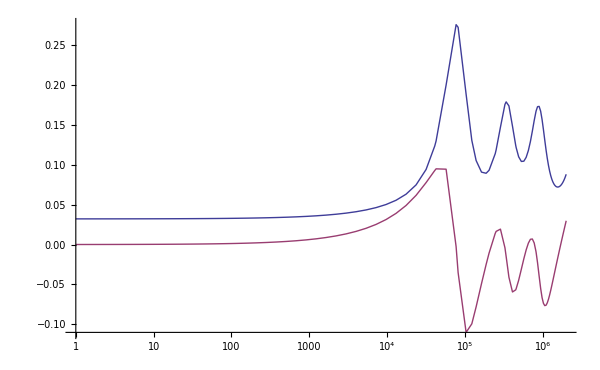

```mathematica
GrPAT=ListLogLinearPlot[{Transpose@{f,Re[1/ZPAT]},Transpose@{f,Im[1/ZPAT]}},Joined->True]
```

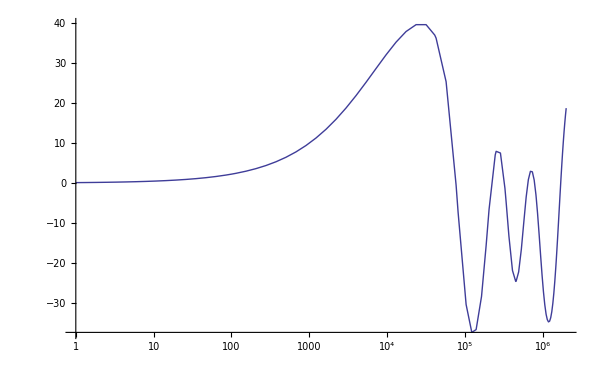

```mathematica
GrPAT=ListLogLinearPlot[Transpose@{f,Arg[1/ZPAT]*180/π},Joined->True]
```

```mathematica
Export["omega.txt",2 π f];
Export["yPAT.txt",YPAT];
Export["zPAT.txt",ZPAT];
```

## Calculo da Matriz de Resistencias SOLO CON ZT (VERIFICACION ZT)

```mathematica
ω=2 π 60;
```

```mathematica
aux=PadRight[matrizZT,{segstotal,segstotal+1},{-1.}];
matrizR=PadRight[aux,{segstotal+1,segstotal+1},{1.}];
matrizR[[segstotal+1,segstotal+1]]=0;
```

```mathematica
resp=Flatten[{0*Range[1,segstotal],1}];
corrdist=LinearSolve[matrizR,resp];
RPAT=corrdist[[segstotal+1]]/1
```

30.564+0.844584 ⅈ

## Calculo da Matriz de Resistencias (POTENCIALES SEGMENTO-PONTO)

```mathematica
matrizA=Table[0,{segstotal},{segstotal}];
aux1={0,0,#}&/@(2*Abs[SP1GM[[All,3]]]);
aux2={0,0,#}&/@(2*Abs[SP2GM[[All,3]]]);
```

```mathematica
Punto=Table[SPGMXI[[#]],{segstotal}]&/@Range[1,segstotal];
Timing[Table[R1=Norm[(SP1GM-Punto[[p]])[[#,All]]]&/@Range[1,segstotal];
R2=Norm[(SP2GM-Punto[[p]])[[#,All]]]&/@Range[1,segstotal];
R1b=Norm[(SP1GM-Punto[[p]]+aux1)[[#,All]]]&/@Range[1,segstotal];
R2b=Norm[(SP2GM-Punto[[p]]+aux2)[[#,All]]]&/@Range[1,segstotal];
T1=Log[(R1+R2+LSmatriz)/(R1+R2-LSmatriz)];
T1b=Log[(R1b+R2b+LSmatriz)/(R1b+R2b-LSmatriz)];
matrizA[[p]]=ro2*(T1[[#]]+T1b[[#]])/LSmatriz[[#]]&/@Range[1,segstotal],{p,1,segstotal}];]
```

{0.19585,Null}

```mathematica
aux=PadRight[matrizA/(4 π),{segstotal,segstotal+1},{-1.}];
matrizR=PadRight[aux,{segstotal+1,segstotal+1},{1.}];
matrizR[[segstotal+1,segstotal+1]]=0;
```

```mathematica
resp=Flatten[{0*Range[1,segstotal],1}];
corrdist=LinearSolve[matrizR,resp];
RPAT=corrdist[[segstotal+1]]/1
```

31.349